## Metricas del fluido perfecto e indice del politropo

```mathematica
ξ[r_]:=Log[(A-(B)*(r^2))^2];
μ[r_]:=-Log[1+(c)(r^2)((A)-3(r^2)(B))^(-2/3)];
Γ:=1+1/n
```

## Ecuación diferencial master para la obtención de la deformación del espacio f

```mathematica
DSolve[f'[r]/r+f[r]/r^2==-(Ka)^(Γ)(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)),f[r],r]
```

{{f[r]→(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))+C[1]/r}}

```mathematica
f[r_]:=(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))
```

## Ecuación diferencial para la obtención de la derivada de la deformación del tiempo

```mathematica
gprime[r_]:=(r/(Exp[-μ[r]]+f[r]))(κ Ka((Ka)^(Γ)/κ(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)))^(Γ) -f[r](1/r^2+ξ'[r]/r))
```

```mathematica
gprime[r]//FullSimplify
```

(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
gprime[r_]:=(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

```mathematica
gprime[r]/.{M->u R,r->x R}//FullSimplify
```

(R x (-(c Ka^(1+1/n) (A-5 B R^2 x^2))/((A-3 B R^2 x^2)^(2/3) (A-B R^2 x^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B R^2 x^2))/((A-3 B R^2 x^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) R^2 x^2)/((A-3 B R^2 x^2)^(2/3)))

```mathematica
gprimeg[x_]:=(x (2.6954227329125043*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3.+((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.031143345546225068+0.15699457419202642 √(1-2. u)+0.15571672773112535 x^2))/((0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2))))/(1-(2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2)/((0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)))
```

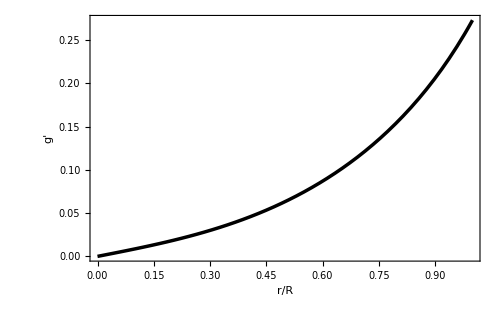

```mathematica
solu1:=Re[gprimeg[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","g'"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

## Cambio en la geometria del espacio-tiempo

### Derivada de ν, para el tiempo

```mathematica
νprime[r_]:=D[ξ[r],r]+gprime[r]
νprime[r]//FullSimplify
```

-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
νprime[r_]:=-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

### Cambio de λ, para el espacio

```mathematica
λ[r_]:=-Log[Exp[-μ[r]]+f[r]]
```

```mathematica
λ[r]//FullSimplify
```

-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))]

```mathematica
λ[r_]:=-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))];
```

## Ecuaciones de Einstein

### Densidad Efectiva

```mathematica
ρ[r_]:=1/(κ r^2)(1-ⅇ^(-λ[r])(1-r D[λ[r],r]));
ρ[r]//FullSimplify
```

-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ)

```mathematica
ρ[r_]:=-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ);
```

### Presión efectiva

```mathematica
Pr[r_]:=-1/(κ r^2)(1-ⅇ^(-λ[r])(1+r *νprime[r]));
Pr[r]//FullSimplify
```

(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)/((A-3 B r^2) (A-B r^2) κ)

```mathematica
Pr[r_]:=(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)/((A-3 B r^2) (A-B r^2) κ)
```

### Presión Tangencial efectiva

```mathematica
Pt[r_]:=Exp[-λ[r]]/(4κ)(2νprime'[r]+(νprime[r])^2-λ'[r]νprime[r]+(2(νprime[r]-λ'[r]))/r);
Pt[r]//Simplify
```

((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)

```mathematica
Pt[r_]:=((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)
```

## Resolución de la integral numérica de gprima, mediante MATLAB

```mathematica
gnume:=-1.638205905918278
```

```mathematica
νnumer[r_]:=ξ[r]+gnume
```

## Aplicación de las condiciones de frontera

```mathematica
Solve[Exp[-λ[R]]==1-(2M)/R,c]
```

{{c→-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)}}

```mathematica
c:=-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)
```

```mathematica
NSolve[Exp[νnumer[R]]==1-(2M)/R,A]
```

{{A→9.48566×10^-8 (1.05422×10^7 B R^2-(2.39147×10^7 √(-2. M+R))/(√R))},{A→9.48566×10^-8 (1.05422×10^7 B R^2+(2.39147×10^7 √(-2. M+R))/(√R))}}

```mathematica
A:=9.485659106280171*^-8 (1.054223*^7 B R^2-(2.39146692940399*^7 √(-2. M+R))/(√R))
Pr[R]//FullSimplify
```

(8. B^2 R^6+9.07386 B R^(7/2) √(-2. M+R)+(M (20.5837 M-10.2919 R-16. B^2 R^5-27.2216 B R^(5/2) √(-2. M+R)))/(1.+Ka^(1+1/n))+(Ka^(2+1/n) M (-61.7511 M+30.8756 R+9.07386 B R^(5/2) √(-2. M+R)) ((Ka^(1+1/n) M (2. B R^(5/2)+6.80539 √(-2. M+R)))/((1.+Ka^(1+1/n)) R^3 (1. B R^(5/2)+1.13423 √(-2. M+R)) κ))^(1/n))/(1.+Ka^(1+1/n)))/(R^3 (-10.2919 M+5.14593 R+4.53693 B R^(5/2) √(-2. M+R)) κ)

### Damos las constantes que usamos en la integración

```mathematica
B=0.45;
Ka=0.44;
n=0.5;
κ=8*π;
R=1;
```

```mathematica
Pr[r]/. {M->u R}
```

(2.43 r^2-1.70742×10^-7 (4.744×10^6-2.39147×10^7 √(1-2. u))-1.84301 (-1.35+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u)))^(2/3) (-2.25 r^2+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u))) (-1.35 r^2+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u)))^(1/3) u+2.69542×10^-6 (-1.35 r^2+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u))) (-0.45 r^2+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u))) (((-1.35+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u)))^(2/3) (-2.25 r^2+2.8457×10^-7 (4.744×10^6-2.39147×10^7 √(1-2. u))) u)/(-1.35 r^2+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u)))^(5/3))^3.)/(8 π (-1.35 r^2+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u))) (-0.45 r^2+9.48566×10^-8 (4.744×10^6-2.39147×10^7 √(1-2. u))))

```mathematica
Pr[r_]:=(2.43 r^2-1.7074186391304309*^-7 (4.7440035*^6-2.39146692940399*^7 √(1-2. u))-1.8430054258079738 (-1.35+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u)))^(2/3) (-2.25 r^2+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u))) (-1.35 r^2+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u)))^(1/3) u+2.6954227329125043*^-6 (-1.35 r^2+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u))) (-0.45 r^2+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u))) (((-1.35+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u)))^(2/3) (-2.25 r^2+2.8456977318840515*^-7 (4.7440035*^6-2.39146692940399*^7 √(1-2. u))) u)/(-1.35 r^2+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u)))^(5/3))^3.)/(8 π (-1.35 r^2+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u))) (-0.45 r^2+9.485659106280171*^-8 (4.7440035*^6-2.39146692940399*^7 √(1-2. u))))
```

```mathematica
NSolve[Pr[R]==0,u]
```

```mathematica
{{u->0.49740143621256666},{u->0.30291735630467564}}
```

```mathematica
u=0.30291735630467564
```

0.302917

## Intercambio Energético

```mathematica
DEnergy[r_]:=gprime[r]/(2κ)×Exp[-μ[r]]/r(ξ'[r]+μ'[r])
DEnergy[r]/.{M->u R,r->x R}//FullSimplify
```

1/(16 (π+((1.66977-2.89212 ⅈ) x^2)/((-0.9742-1.35 x^2)^(2/3))))(1+((0.489782-0.848328 ⅈ) x^2)/((-0.9742-1.35 x^2)^(2/3))) (2.69542×10^-6 (-((0.265752-0.460296 ⅈ) (-2.9226-2.25 x^2))/((-0.9742-1.35 x^2)^(5/3)))^3.-((0.0417216-0.072264 ⅈ) (-0.9742-2.25 x^2))/((-0.9742-1.35 x^2)^(2/3) (-0.9742-0.45 x^2))) ((4. x)/(2.16489+1. x^2)+((-0.706883+1.22436 ⅈ) x-(0.326522-0.565552 ⅈ) x^3)/((0.72163+1. x^2) ((0.489782-0.848328 ⅈ) x^2+(-0.9742-1.35 x^2)^(2/3))))

```mathematica
DEnergy[x_]:=1/(16 (π+((1.6697690314845368-2.8921247994362957 ⅈ) x^2)/((-0.9742003234898915-1.35 x^2)^(2/3))))(1+((0.4897823690406985-0.8483279478299403 ⅈ) x^2)/((-0.9742003234898915-1.35 x^2)^(2/3))) (2.6954227329125043*^-6 (-((0.2657519951825307-0.4602959578689429 ⅈ) (-2.922600970469675-2.25 x^2))/((-0.9742003234898915-1.35 x^2)^(5/3)))^3.-((0.04172162132436286-0.07226396790794562 ⅈ) (-0.9742003234898915-2.25 x^2))/((-0.9742003234898915-1.35 x^2)^(2/3) (-0.9742003234898915-0.45 x^2))) ((4. x)/(2.1648896077553146+1. x^2)+((-0.7068831738653245+1.2243575721502868 ⅈ) x-(0.3265215793604658-0.5655519652199604 ⅈ) x^3)/((0.7216298692517714+1. x^2) ((0.4897823690406985-0.8483279478299403 ⅈ) x^2+(-0.9742003234898915-1.35 x^2)^(2/3))))
```

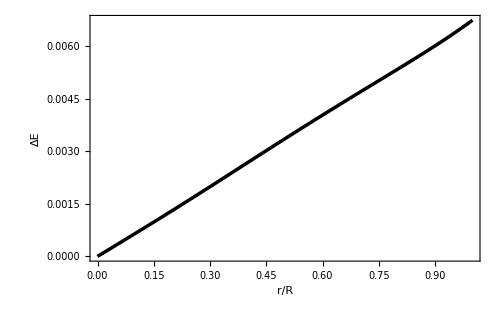

```mathematica
solu1:=Re[DEnergy[x]]
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ΔE"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
DEnergy[x]/.{x->√(x^2+y^2)}//FullSimplify
```

-((7.71481×10^-9 √(x^2+y^2) ((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (((-0.9-2.26846 √(1-2. u))^(2/3) u (-0.595116+3. √(1-2. u)+0.991861 (x^2+y^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.198372+1. √(1-2. u)+0.595116 (x^2+y^2))))^3. (-1.+5.04103 √(1-2. u)+1. (x^2+y^2))+(-0.9-2.26846 √(1-2. u))^(2/3) u (-58244.9+293614. √(1-2. u)+291224. (x^2+y^2))) (10.1648 (-0.9-2.26846 √(1-2. u))^(2/3) u^2+(0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.217037-1.09409 √(1-2. u)-0.65111 (x^2+y^2))+(-0.9-2.26846 √(1-2. u))^(2/3) u (-5.2824+2.01641 √(1-2. u)-1.2437×10^-16 √(1-2. u) (x^2+y^2)+1. (x^2+y^2)^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.198372-1. √(1-2. u)-0.198372 (x^2+y^2))^2 (-0.198372+1. √(1-2. u)+0.595116 (x^2+y^2)) (-2. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)+1. (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))

```mathematica
dEnergy[x_,y_]:=-((7.714814869352783*^-9 √(x^2+y^2) ((0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.5951163415647547+3.0000000000000004 √(1-2. u)+0.991860569274591 (x^2+y^2)))/((0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 (x^2+y^2))))^3. (-1.+5.041031123615297 √(1-2. u)+1. (x^2+y^2))+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-58244.88020934214+293614.25392653834 √(1-2. u)+291224.4010467107 (x^2+y^2))) (10.164797915703241 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u^2+(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.21703679999999986-1.0940892637698683 √(1-2. u)-0.6511104 (x^2+y^2))+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-5.28239895785162+2.016412449446119 √(1-2. u)-1.243704182508828*^-16 √(1-2. u) (x^2+y^2)+1. (x^2+y^2)^2)))/((0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 (x^2+y^2))^2 (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 (x^2+y^2)) (-2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)+1. (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))
```

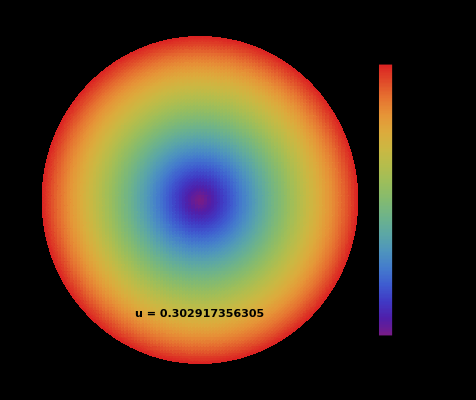

```mathematica
DensityPlot[Re[dEnergy[x,y]]/.{u->0.302917356305},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.302917356305",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Condiciones de aceptabilidad

### Sector material

```mathematica
Pr[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.00773208 (-0.81+4.08324 √(1-2. u)+2.43 x^2+0.0000138705 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.198372+1. √(1-2. u)+0.198372 x^2) (-0.198372+1. √(1-2. u)+0.595116 x^2)+(-0.9-2.26846 √(1-2. u))^(2/3) u (0.45-2.26846 √(1-2. u)-1.35 x^2)^(1/3) (-0.829352+4.18079 √(1-2. u)+4.14676 x^2)))/((-0.198372+1. √(1-2. u)+0.198372 x^2) (-0.198372+1. √(1-2. u)+0.595116 x^2))

```mathematica
Prg[x_]:=(0.0077320802909626556 (-0.81+4.083235210128391 √(1-2. u)+2.43 x^2+0.000013870453859833131 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2) (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 x^2)+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(1/3) (-0.8293524416135881+4.180791470620436 √(1-2. u)+4.1467622080679405 x^2)))/((-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2) (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 x^2))
```

```mathematica
Solve[Prg[1]==0,u]
```

{{u→-166.09},{u→0.302917},{u→0.497401},{u→159.266-7.07042 ⅈ},{u→159.266+7.07042 ⅈ}}

```mathematica
Prg[1]/.u->0.302917356305
```

6.20499×10^-14

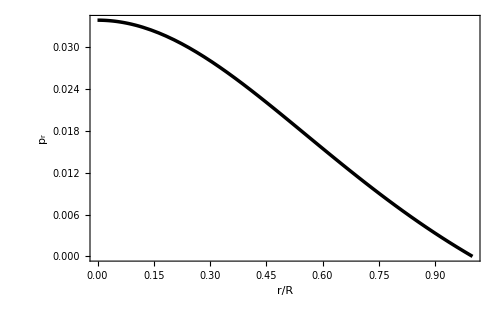

```mathematica
solu1:=Re[Prg[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Full]
```

```mathematica
Pt[r]/.{M-> u R, r->x R}//Simplify
```

(0.00018782 (1-(2. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2)/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3))) (-33.3456 x^2 (0.198372-1. √(1-2. u)-0.595116 x^2)^2 (1. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3))^2+84.0482 (0.198372-1. √(1-2. u)-0.595116 x^2)^2 (-0.198372+1. √(1-2. u)+0.198372 x^2) (1. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3))^2+0.28259 (-0.9-2.26846 √(1-2. u))^(2/3) u x^2 (-2. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2+(0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3)) (-11.6734 (-0.198372+1. √(1-2. u))^3-20.841 (0.198372-1. √(1-2. u))^2 x^2-10.5654 (-0.198372+1. √(1-2. u)) x^4-1.36688 x^6+23.3467 (-0.198372+1. √(1-2. u)) (0.198372-1. √(1-2. u)-0.595116 x^2)^2-0.00300628 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^2. (-0.198372+1. √(1-2. u)+0.198372 x^2)^3)+0.5 x^2 (0.45-2.26846 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9-2.26846 √(1-2. u))^(2/3) u x^2-1.8 (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3)-6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3) (-0.198372+1. √(1-2. u)+0.198372 x^2)-0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 x^2))^2-4. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2 (0.45-2.26846 √(1-2. u)-1.35 x^2) (0.45-2.26846 √(1-2. u)-0.45 x^2)^2 (6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3) (-0.198372+1. √(1-2. u)+0.198372 x^2)+0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 x^2))-1. (0.45-2.26846 √(1-2. u)-1.35 x^2)^2 (0.45-2.26846 √(1-2. u)-0.45 x^2) (-2. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2+(0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3)) (6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3) (-0.198372+1. √(1-2. u)+0.198372 x^2)+0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 x^2))+2. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2 (0.45-2.26846 √(1-2. u)-1.35 x^2) (0.45-2.26846 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9-2.26846 √(1-2. u))^(2/3) u x^2+1.8 (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3)+6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3) (-0.198372+1. √(1-2. u)+0.198372 x^2)+0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 x^2))-1. (0.45-2.26846 √(1-2. u)-1.35 x^2) (0.45-2.26846 √(1-2. u)-0.45 x^2) (-2. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2+(0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3)) (20.5837 (-0.9-2.26846 √(1-2. u))^(2/3) u (0.198372-1. √(1-2. u)-0.198372 x^2)^2+8.16647 (-0.198372+1. √(1-2. u)+0.595116 x^2) (1. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-2.26846 √(1-2. u)-1.35 x^2) (6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3) (-0.198372+1. √(1-2. u)+0.198372 x^2)+0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 x^2)))))/((0.198372-1. √(1-2. u)-0.595116 x^2)^2 (0.198372-1. √(1-2. u)-0.198372 x^2)^2 (1. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3))^2)

```mathematica
Ptg[x_]:=(0.00018782032296468958 (1-(2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2)/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)) (-33.34561956246449 x^2 (0.1983721138549182-1. √(1-2. u)-0.5951163415647547 x^2)^2 (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3))^2+84.04815302530929 (0.1983721138549182-1. √(1-2. u)-0.5951163415647547 x^2)^2 (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2) (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3))^2+0.2825902335456476 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2 (-2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2+(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)) (-11.673354586848513 (-0.1983721138549182+1. √(1-2. u))^3-20.8410122265403 (0.1983721138549182-1. √(1-2. u))^2 x^2-10.56537110620721 (-0.1983721138549182+1. √(1-2. u)) x^4-1.366875 x^6+23.346709173697025 (-0.1983721138549182+1. √(1-2. u)) (0.1983721138549182-1. √(1-2. u)-0.5951163415647547 x^2)^2-0.003006278288724897 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^2. (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2)^3)+0.5 x^2 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2-1.8 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)-6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2)-0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 x^2))^2-4. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2) (0.45-2.2684640056268837 √(1-2. u)-0.45 x^2)^2 (6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2)+0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 x^2))-1. (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^2 (0.45-2.2684640056268837 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2+(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)) (6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2)+0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 x^2))+2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2) (0.45-2.2684640056268837 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2+1.8 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)+6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2)+0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 x^2))-1. (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2) (0.45-2.2684640056268837 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2+(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)) (20.583715779299066 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 x^2)^2+8.16647042025678 (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 x^2) (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2) (6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2)+0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 x^2)))))/((0.1983721138549182-1. √(1-2. u)-0.5951163415647547 x^2)^2 (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 x^2)^2 (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3))^2)
```

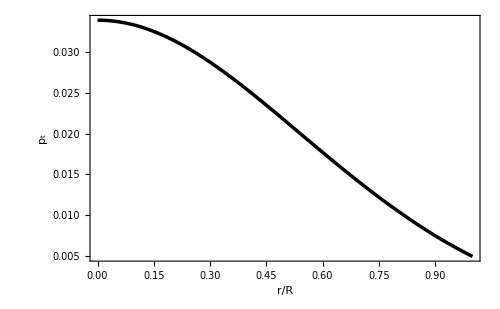

```mathematica
solu1:=Re[Ptg[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
ρ[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.0795775 (-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3))

```mathematica
ρg[x_]:=(0.07957747154594767 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3)
```

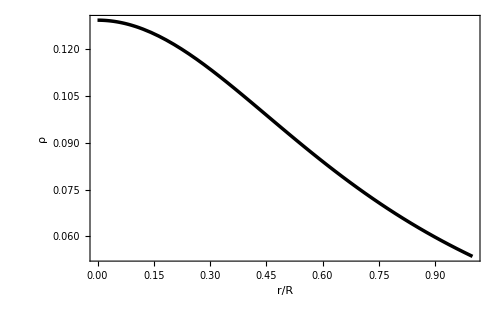

```mathematica
solu1:=Re[ρg[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Gráficas de componentes metricas del espacio-tiempo

```mathematica
Exp[νnumer[r]]/.{M->u R,r->x R}//FullSimplify
```

1. (0.198372-1. √(1-2. u)-0.198372 x^2)^2

```mathematica
metric1[x_]:=1. (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 x^2)^2
```

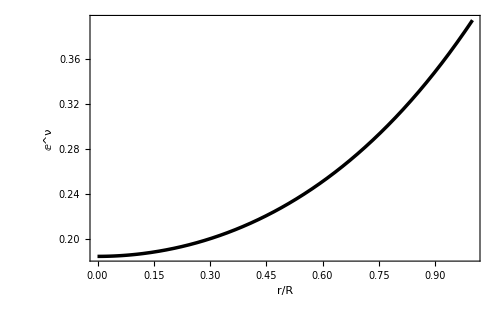

```mathematica
solu1:=Re[metric1[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^ν"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Exp[-λ[r]]/.{M-> u R, r->x R}//FullSimplify
```

1-(2. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2)/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3))

```mathematica
metric2[x_]:=1-(2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2)/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)
```

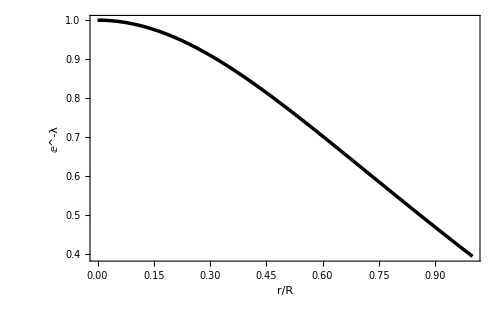

```mathematica
solu1:=Re[metric2[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^-λ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condiciones de energía

#### Condición de energía dominante

```mathematica
dec1[x_]:=ρg[x]-Prg[x];
```

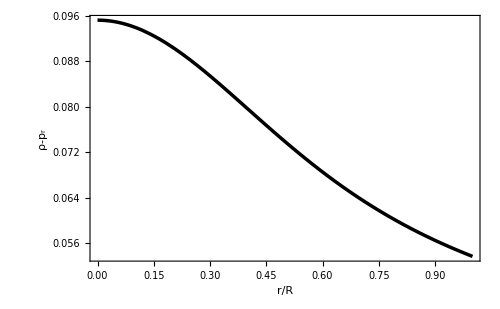

```mathematica
solu1:=Re[dec1[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
dec2[x_]:=ρg[x]-Ptg[x];
```

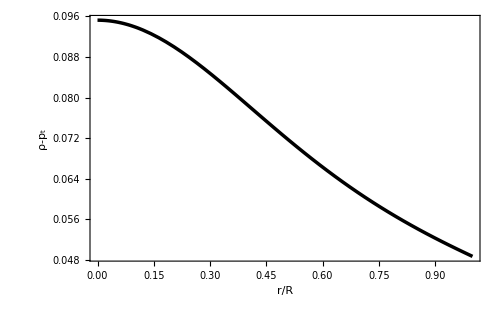

```mathematica
solu1:=Re[dec2[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Condicion de energía fuerte

```mathematica
sec[x_]:=ρg[x]-Prg[x]-2*Ptg[x];
```

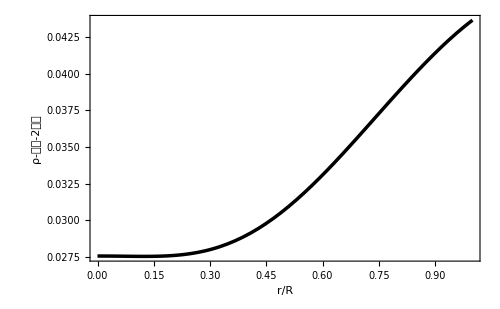

```mathematica
solu1:=Re[sec[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-𝓅𝓇-2𝓅𝓉"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Corrimiento al rojo

```mathematica
Z[r_]:=1/(√(ⅇ^(νnumer[r])))-1
```

```mathematica
Z[r]/.{M-> u R, r->x R}//FullSimplify
```

-1+1./(√((0.198372-1. √(1-2. u)-0.198372 x^2)^2))

```mathematica
Z[x_]:=-1+1./(√(0.1983721138549182-1. √(1-2. u)-0.1983721138549182 x^2)^2)
```

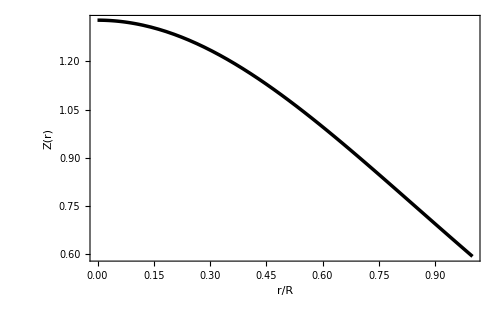

```mathematica
solu1:=Re[Z[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Z(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condición de causalidad:?

#### Velocidad Radial?

```mathematica
vr[r_]:=D[Pr[r],r]/D[ρ[r],r]
```

```mathematica
vr[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.00472044 (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-2.26846 √(1-2. u)-1.35 x^2) (0.45-2.26846 √(1-2. u)-0.45 x^2) (4.86+((-0.9-2.26846 √(1-2. u))^(2/3) u (0.746417-3.76271 √(1-2. u)-3.73209 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3))+8.29352 (-0.9-2.26846 √(1-2. u))^(2/3) u (0.45-2.26846 √(1-2. u)-1.35 x^2)^(1/3)+0.0000165091 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.198372+1. √(1-2. u)+0.198372 x^2)-(0.0000550302 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.198372-1. √(1-2. u)-0.198372 x^2)^2)/(-0.198372+1. √(1-2. u)+0.33062 x^2)+5.50302×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.198372+1. √(1-2. u)+0.595116 x^2))+0.286479 (0.45-2.26846 √(1-2. u)-1.35 x^2) (-0.81+4.08324 √(1-2. u)+2.43 x^2+0.0000138705 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.198372+1. √(1-2. u)+0.198372 x^2) (-0.198372+1. √(1-2. u)+0.595116 x^2)+(-0.9-2.26846 √(1-2. u))^(2/3) u (0.45-2.26846 √(1-2. u)-1.35 x^2)^(1/3) (-0.829352+4.18079 √(1-2. u)+4.14676 x^2))+0.859437 (0.45-2.26846 √(1-2. u)-0.45 x^2) (-0.81+4.08324 √(1-2. u)+2.43 x^2+0.0000138705 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 x^2))/((0.45-2.26846 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.198372+1. √(1-2. u)+0.198372 x^2) (-0.198372+1. √(1-2. u)+0.595116 x^2)+(-0.9-2.26846 √(1-2. u))^(2/3) u (0.45-2.26846 √(1-2. u)-1.35 x^2)^(1/3) (-0.829352+4.18079 √(1-2. u)+4.14676 x^2))))/((-0.9-2.26846 √(1-2. u))^(2/3) u (0.198372-1. √(1-2. u)-0.198372 x^2)^2 (0.0626299-0.315719 √(1-2. u)-0.0626299 x^2))

```mathematica
vrg[x_]:= (0.004720439574565849 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2) (0.45-2.2684640056268837 √(1-2. u)-0.45 x^2) (4.86+((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.7464171974522293-3.762712323558393 √(1-2. u)-3.732085987261147 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3)+8.293524416135883 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(1/3)+0.00001650906751381325 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2)-(0.000055030225046044185 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.19837211385491824-1. √(1-2. u)-0.19837211385491818 x^2)^2)/(-0.19837211385491824+1. √(1-2. u)+0.330620189758197 x^2)+5.503022504604416*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 x^2))+0.2864788975654116 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2) (-0.81+4.083235210128391 √(1-2. u)+2.43 x^2+0.000013870453859833131 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2) (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 x^2)+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(1/3) (-0.8293524416135881+4.180791470620436 √(1-2. u)+4.1467622080679405 x^2))+0.8594366926962349 (0.45-2.2684640056268837 √(1-2. u)-0.45 x^2) (-0.81+4.083235210128391 √(1-2. u)+2.43 x^2+0.000013870453859833131 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 x^2))/(0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2) (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 x^2)+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(1/3) (-0.8293524416135881+4.180791470620436 √(1-2. u)+4.1467622080679405 x^2))))/((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 x^2)^2 (0.06262985035679756-0.3157190249159851 √(1-2. u)-0.06262985035679754 x^2))
```

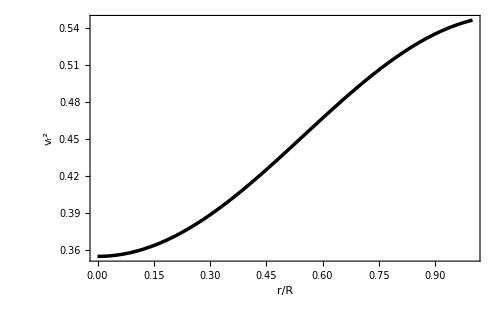

```mathematica
solu1:=vrg[x]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Velocidad Tangencial

```mathematica
vt[r_]:=D[Pt[r],r]/D[ρ[r],r]
vt[r]/.{M-> u R, r->x R}//Simplify
```

-(0.000917315 (0.45-2.26846 √(1-2. u)-1.35 x^2)^(2/3) (0.198372-1. √(1-2. u)-0.595116 x^2)^2 (7+1/x))/((-0.9-2.26846 √(1-2. u))^(2/3) u x (0.0626299-0.315719 √(1-2. u)-0.0626299 x^2) (-0.198372+1. √(1-2. u)+0.198372 x^2)^3 (-0.198372+1. √(1-2. u)+0.595116 x^2)^3 (1. (-0.9-2.26846 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.26846 √(1-1)-1.35 x^2)^(2/3))^3)
 |  |  |  |

```mathematica
vtg[x_]:={{-((0.0009173153429009489 (0.45-2.2684640056268837 √(1-2. u)-1.35 x^2)^(2/3) (0.1983721138549182-1. √(1-2. u)-0.5951163415647547 x^2)^2 (7+1/x))/((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x (0.06262985035679756-0.3157190249159851 √(1-2. u)-0.06262985035679754 x^2) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 x^2)^3 (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 x^2)^3 (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u x^2-0.5 (0.45-2.2684640056268837 √(1-1)-1.35 x^2)^(2/3))^3))}, {{{, , , , }}}}
```

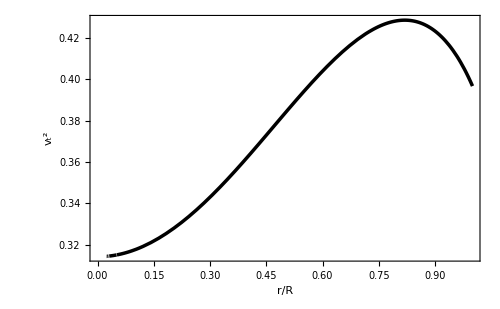

```mathematica
solu1:=vtg[x]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

## Anisotropía

```mathematica
Π[x_]:=Ptg[x]-Prg[x]
```

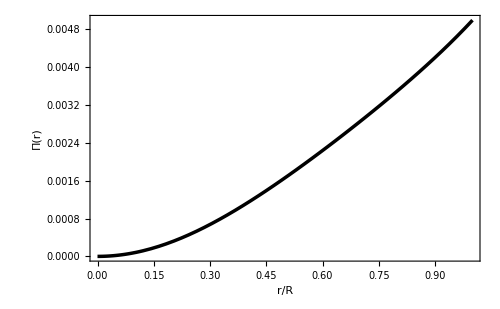

```mathematica
solu1:=Re[Π[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Π(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Π[x]/.{x->√(x^2+y^2)}//Simplify
```

-((0.00773208 (-0.81+4.08324 √(1-2. u)+2.43 (x^2+y^2)+0.0000138705 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2)) (-0.198372+1. √(1-2. u)+0.595116 (x^2+y^2))+(-0.9-2.26846 √(1-2. u))^(2/3) u (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.829352+4.18079 √(1-2. u)+4.14676 (x^2+y^2))))/((-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2)) (-0.198372+1. √(1-2. u)+0.595116 (x^2+y^2))))+(0.00018782 (1-(2. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-33.3456 (x^2+y^2) (0.198372-1. √(1-2. u)-0.595116 (x^2+y^2))^2 (1. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+84.0482 (0.198372-1. √(1-2. u)-0.595116 (x^2+y^2))^2 (-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2)) (1. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.28259 (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-11.6734 (-0.198372+1. √(1-2. u))^3-20.841 (0.198372-1. √(1-2. u))^2 (x^2+y^2)-10.5654 (-0.198372+1. √(1-2. u)) (x^2+y^2)^2-1.36688 (x^2+y^2)^3+23.3467 (-0.198372+1. √(1-2. u)) (0.198372-1. √(1-2. u)-0.595116 (x^2+y^2))^2-0.00300628 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^2. (-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2))^3)+0.5 (x^2+y^2) (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2))-0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 (x^2+y^2)))^2-4. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2)) (0.45-2.26846 √(1-2. u)-0.45 (x^2+y^2))^2 (6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2))+0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 (x^2+y^2)))-1. (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-2.26846 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2))+0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 (x^2+y^2)))+2. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2)) (0.45-2.26846 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2))+0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 (x^2+y^2)))-1. (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2)) (0.45-2.26846 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (20.5837 (-0.9-2.26846 √(1-2. u))^(2/3) u (0.198372-1. √(1-2. u)-0.198372 (x^2+y^2))^2+8.16647 (-0.198372+1. √(1-2. u)+0.595116 (x^2+y^2)) (1. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2)) (6.11447×10^-6 (((-0.9-2.26846 √(1-2. u))^(2/3) u (1.35-6.80539 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.198372+1. √(1-2. u)+0.198372 (x^2+y^2))+0.356137 (-0.9-2.26846 √(1-2. u))^(2/3) u (-0.198372+1. √(1-2. u)+0.991861 (x^2+y^2))))))/((0.198372-1. √(1-2. u)-0.595116 (x^2+y^2))^2 (0.198372-1. √(1-2. u)-0.198372 (x^2+y^2))^2 (1. (-0.9-2.26846 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)

```mathematica
Π[x_,y_]:=-((0.0077320802909626556 (-0.81+4.083235210128391 √(1-2. u)+2.43 (x^2+y^2)+0.000013870453859833131 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2)) (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 (x^2+y^2))+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.8293524416135881+4.180791470620436 √(1-2. u)+4.1467622080679405 (x^2+y^2))))/((-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2)) (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 (x^2+y^2))))+(0.00018782032296468958 (1-(2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-33.34561956246449 (x^2+y^2) (0.1983721138549182-1. √(1-2. u)-0.5951163415647547 (x^2+y^2))^2 (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+84.04815302530929 (0.1983721138549182-1. √(1-2. u)-0.5951163415647547 (x^2+y^2))^2 (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2)) (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.2825902335456476 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-11.673354586848513 (-0.1983721138549182+1. √(1-2. u))^3-20.8410122265403 (0.1983721138549182-1. √(1-2. u))^2 (x^2+y^2)-10.56537110620721 (-0.1983721138549182+1. √(1-2. u)) (x^2+y^2)^2-1.366875 (x^2+y^2)^3+23.346709173697025 (-0.1983721138549182+1. √(1-2. u)) (0.1983721138549182-1. √(1-2. u)-0.5951163415647547 (x^2+y^2))^2-0.003006278288724897 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^2. (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2))^3)+0.5 (x^2+y^2) (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2))-0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 (x^2+y^2)))^2-4. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2)) (0.45-2.2684640056268837 √(1-2. u)-0.45 (x^2+y^2))^2 (6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2))+0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 (x^2+y^2)))-1. (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-2.2684640056268837 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2))+0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 (x^2+y^2)))+2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2)) (0.45-2.2684640056268837 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2))+0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 (x^2+y^2)))-1. (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2)) (0.45-2.2684640056268837 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (20.583715779299066 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 (x^2+y^2))^2+8.16647042025678 (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 (x^2+y^2)) (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2)) (6.1144694495604615*^-6 (((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (1.35-6.805392016880652 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.1983721138549182+1. √(1-2. u)+0.1983721138549182 (x^2+y^2))+0.3561365406333312 (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (-0.1983721138549182+1. √(1-2. u)+0.9918605692745911 (x^2+y^2))))))/((0.1983721138549182-1. √(1-2. u)-0.5951163415647547 (x^2+y^2))^2 (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 (x^2+y^2))^2 (1. (-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)
```

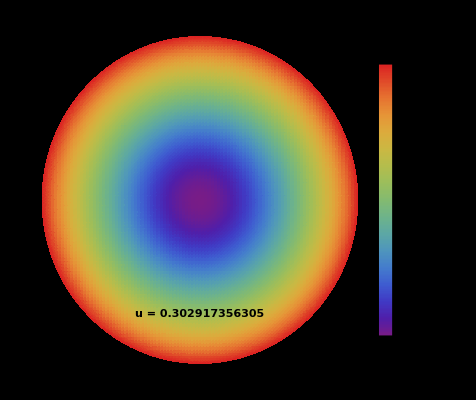

```mathematica
DensityPlot[Re[Π[x,y]]/.{u->0.302917356305},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Magma",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.302917356305",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Cracking Gravitacional

```mathematica
CG[x_]:=vt[x]-vr[x]
```

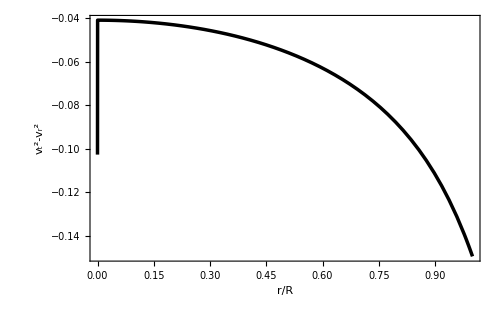

```mathematica
solu1:=Re[CG[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2-v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Limit[CG[x],x->0]/.{u->0.302917356305}
```

-0.0409435-2.77556×10^-15 ⅈ

```mathematica
Re[Limit[CG[x],x->0]]/.{u->0.302917356305}
```

-0.0409435

## Adiabatic index Γ

```mathematica
AI[x_]:=((ρg[x]+Prg[x])/Prg[x])(vrg[x]);
```

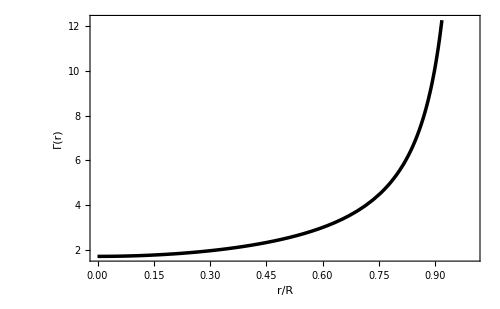

```mathematica
solu1:=Re[AI[x]]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Γ(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Re[AI[0]]/.{u->0.302917356305}
```

1.70947